```mathematica
ClearAll["Global`*"]
```

```mathematica
(* GAPDH Kinetics with 30 mM Tris, 10 mM Arsenate, pH 8.5 by MW-KK 2020 *)(* NAD+ levels are 0.125; 0.250, and 0.500 mM *)
cGAP={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800};
cNAD ={{0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125},{0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25},{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}};
v125={0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188};
v250={0.050,0.104,0.150,0.182,0.237,0.241,0.264,0.259,0.266,0.232};
v500={0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.310,0.334,0.322};
```

```mathematica
cGADs=Transpose[{cGAP,cNAD[[1]]}],Transpose[{cGAP,cNAD[[2]]}],Transpose[{cGAP,cNAD[[3]]},{2,1}]

TraTra
```

```mathematica
vNADS={{0.125,v125},{0.250,v250},{0.500,v500}}
```

{{0.125,{0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188}},{0.25,{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}},{0.5,{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}}}

```mathematica
vNAD= {v125,v250,v500}
```

{{0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188},{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232},{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}}

```mathematica
{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}
```

{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}

```mathematica
FittedModels`[{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}
```

```mathematica
FittedModel
```

FittedModel

```mathematica
test1={{0.125,0.05,0.039},{0.125,0.1,0.095},{0.125,0.2,0.129},{0.125,0.3,0.171},{0.125,0.5,0.188},{0.125,0.7,0.182},{0.125,0.9,0.192},{0.125,1.1,0.206},{0.125,1.4,0.187},{0.125,1.8,0.188}}
```

{{0.125,0.05,0.039},{0.125,0.1,0.095},{0.125,0.2,0.129},{0.125,0.3,0.171},{0.125,0.5,0.188},{0.125,0.7,0.182},{0.125,0.9,0.192},{0.125,1.1,0.206},{0.125,1.4,0.187},{0.125,1.8,0.188}}

```mathematica
Flatten[test1]
```

{0.125,0.05,0.039,0.125,0.1,0.095,0.125,0.2,0.129,0.125,0.3,0.171,0.125,0.5,0.188,0.125,0.7,0.182,0.125,0.9,0.192,0.125,1.1,0.206,0.125,1.4,0.187,0.125,1.8,0.188}

```mathematica
Fit[{0.125,0.05,0.039,0.125,0.1,0.095,0.125,0.2,0.129,0.125,0.3,0.171,0.125,0.5,0.188,0.125,0.7,0.182,0.125,0.9,0.192,0.125,1.1,0.206,0.125,1.4,0.187,0.125,1.8,0.188},{1,x},x]
```

-0.0224391+0.0226885 x

```mathematica
FittedModel[…]
```

FittedModel[…]

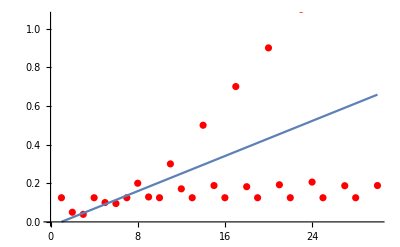

```mathematica
Show[ListPlot[{0.125,0.05,0.039,0.125,0.1,0.095,0.125,0.2,0.129,0.125,0.3,0.171,0.125,0.5,0.188,0.125,0.7,0.182,0.125,0.9,0.192,0.125,1.1,0.206,0.125,1.4,0.187,0.125,1.8,0.188},PlotStyle->Red],Plot[-0.022439080459770028+0.022688542825361507 x,{x,1,30}]]
```

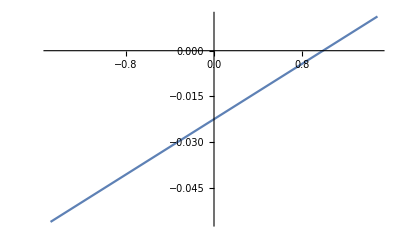

```mathematica
Plot[-0.022439080459770028+0.022688542825361507 x,{x,-1.4835073785360535,1.4835073785360535}]
```

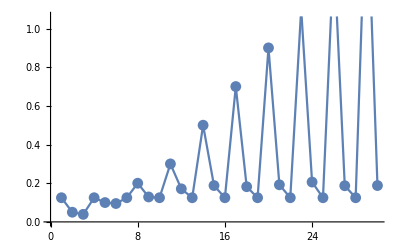

```mathematica
ListLinePlot[{0.125,0.05,0.039,0.125,0.1,0.095,0.125,0.2,0.129,0.125,0.3,0.171,0.125,0.5,0.188,0.125,0.7,0.182,0.125,0.9,0.192,0.125,1.1,0.206,0.125,1.4,0.187,0.125,1.8,0.188},Mesh->All]
```

```mathematica
Fit[{0.125,0.05,0.039,0.125,0.1,0.095,0.125,0.2,0.129,0.125,0.3,0.171,0.125,0.5,0.188,0.125,0.7,0.182,0.125,0.9,0.192,0.125,1.1,0.206,0.125,1.4,0.187,0.125,1.8,0.188},{1,x},x]
```

-0.0224391+0.0226885 x

```mathematica
(FunctionInterpolation[#1,{x,-1.4835073785360535,1.4835073785360535}]&)[-0.022439080459770028+0.022688542825361507 x]
```

InterpolatingFunction[…]

```mathematica
Plot[-0.022439080459770028+0.022688542825361507 x,{x,-1.4835073785360535,1.4835073785360535}]
```

-Graphics-

```mathematica
ListPointPlot3D[test1]
```

-Graphics3D-

```mathematica
Union@@%265
```

{0.039,0.044,0.05,0.095,0.1,0.103,0.104,0.125,0.129,0.15,0.161,0.171,0.182,0.187,0.188,0.192,0.2,0.206,0.212,0.232,0.237,0.241,0.25,0.259,0.264,0.266,0.287,0.293,0.3,0.31,0.322,0.334,0.5,0.7,0.9,1.1,1.4,1.8}

```mathematica
Sort/@%265
```

{{0.039,0.05,0.125},{0.05,0.05,0.25},{0.044,0.05,0.5},{0.095,0.1,0.125},{0.1,0.104,0.25},{0.1,0.103,0.5},{0.125,0.129,0.2},{0.15,0.2,0.25},{0.161,0.2,0.5},{0.125,0.171,0.3},{0.182,0.25,0.3},{0.212,0.3,0.5},{0.125,0.188,0.5},{0.237,0.25,0.5},{0.266,0.5,0.5},{0.125,0.182,0.7},{0.241,0.25,0.7},{0.287,0.5,0.7},{0.125,0.192,0.9},{0.25,0.264,0.9},{0.293,0.5,0.9},{0.125,0.206,1.1},{0.25,0.259,1.1},{0.31,0.5,1.1},{0.125,0.187,1.4},{0.25,0.266,1.4},{0.334,0.5,1.4},{0.125,0.188,1.8},{0.232,0.25,1.8},{0.322,0.5,1.8}}

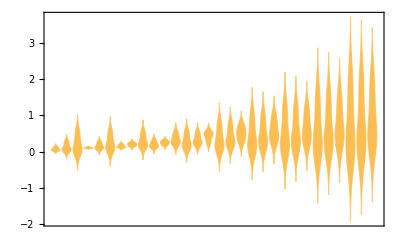

```mathematica
DistributionChart[%265]
```

```mathematica
RowReduce[%265]
```

{{1,0.,0.},{0,1,0.},{0,0,1},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
MatrixForm[%265]
```

(0.125 | 0.05 | 0.039
0.25 | 0.05 | 0.05
0.5 | 0.05 | 0.044
0.125 | 0.1 | 0.095
0.25 | 0.1 | 0.104
0.5 | 0.1 | 0.103
0.125 | 0.2 | 0.129
0.25 | 0.2 | 0.15
0.5 | 0.2 | 0.161
0.125 | 0.3 | 0.171
0.25 | 0.3 | 0.182
0.5 | 0.3 | 0.212
0.125 | 0.5 | 0.188
0.25 | 0.5 | 0.237
0.5 | 0.5 | 0.266
0.125 | 0.7 | 0.182
0.25 | 0.7 | 0.241
0.5 | 0.7 | 0.287
0.125 | 0.9 | 0.192
0.25 | 0.9 | 0.264
0.5 | 0.9 | 0.293
0.125 | 1.1 | 0.206
0.25 | 1.1 | 0.259
0.5 | 1.1 | 0.31
0.125 | 1.4 | 0.187
0.25 | 1.4 | 0.266
0.5 | 1.4 | 0.334
0.125 | 1.8 | 0.188
0.25 | 1.8 | 0.232
0.5 | 1.8 | 0.322)

```mathematica
Transpose[%293]
```

{{0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5},{0.05,0.05,0.05,0.1,0.1,0.1,0.2,0.2,0.2,0.3,0.3,0.3,0.5,0.5,0.5,0.7,0.7,0.7,0.9,0.9,0.9,1.1,1.1,1.1,1.4,1.4,1.4,1.8,1.8,1.8},{0.039,0.05,0.044,0.095,0.104,0.103,0.129,0.15,0.161,0.171,0.182,0.212,0.188,0.237,0.266,0.182,0.241,0.287,0.192,0.264,0.293,0.206,0.259,0.31,0.187,0.266,0.334,0.188,0.232,0.322}}

```mathematica
Flatten[%295]
```

{0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.05,0.05,0.05,0.1,0.1,0.1,0.2,0.2,0.2,0.3,0.3,0.3,0.5,0.5,0.5,0.7,0.7,0.7,0.9,0.9,0.9,1.1,1.1,1.1,1.4,1.4,1.4,1.8,1.8,1.8,0.039,0.05,0.044,0.095,0.104,0.103,0.129,0.15,0.161,0.171,0.182,0.212,0.188,0.237,0.266,0.182,0.241,0.287,0.192,0.264,0.293,0.206,0.259,0.31,0.187,0.266,0.334,0.188,0.232,0.322}

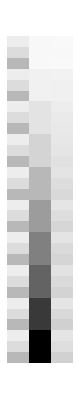

```mathematica
ArrayPlot[%293]
```

```mathematica
Transpose[%265]
```

{{0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5},{0.05,0.05,0.05,0.1,0.1,0.1,0.2,0.2,0.2,0.3,0.3,0.3,0.5,0.5,0.5,0.7,0.7,0.7,0.9,0.9,0.9,1.1,1.1,1.1,1.4,1.4,1.4,1.8,1.8,1.8},{0.039,0.05,0.044,0.095,0.104,0.103,0.129,0.15,0.161,0.171,0.182,0.212,0.188,0.237,0.266,0.182,0.241,0.287,0.192,0.264,0.293,0.206,0.259,0.31,0.187,0.266,0.334,0.188,0.232,0.322}}

```mathematica
TableForm[%265]
```

0.125 | 0.05 | 0.039
0.25 | 0.05 | 0.05
0.5 | 0.05 | 0.044
0.125 | 0.1 | 0.095
0.25 | 0.1 | 0.104
0.5 | 0.1 | 0.103
0.125 | 0.2 | 0.129
0.25 | 0.2 | 0.15
0.5 | 0.2 | 0.161
0.125 | 0.3 | 0.171
0.25 | 0.3 | 0.182
0.5 | 0.3 | 0.212
0.125 | 0.5 | 0.188
0.25 | 0.5 | 0.237
0.5 | 0.5 | 0.266
0.125 | 0.7 | 0.182
0.25 | 0.7 | 0.241
0.5 | 0.7 | 0.287
0.125 | 0.9 | 0.192
0.25 | 0.9 | 0.264
0.5 | 0.9 | 0.293
0.125 | 1.1 | 0.206
0.25 | 1.1 | 0.259
0.5 | 1.1 | 0.31
0.125 | 1.4 | 0.187
0.25 | 1.4 | 0.266
0.5 | 1.4 | 0.334
0.125 | 1.8 | 0.188
0.25 | 1.8 | 0.232
0.5 | 1.8 | 0.322

```mathematica
TableForm[%289]
```

0.125 | 0.05 | 0.039
0.25 | 0.05 | 0.05
0.5 | 0.05 | 0.044
0.125 | 0.1 | 0.095
0.25 | 0.1 | 0.104
0.5 | 0.1 | 0.103
0.125 | 0.2 | 0.129
0.25 | 0.2 | 0.15
0.5 | 0.2 | 0.161
0.125 | 0.3 | 0.171
0.25 | 0.3 | 0.182
0.5 | 0.3 | 0.212
0.125 | 0.5 | 0.188
0.25 | 0.5 | 0.237
0.5 | 0.5 | 0.266
0.125 | 0.7 | 0.182
0.25 | 0.7 | 0.241
0.5 | 0.7 | 0.287
0.125 | 0.9 | 0.192
0.25 | 0.9 | 0.264
0.5 | 0.9 | 0.293
0.125 | 1.1 | 0.206
0.25 | 1.1 | 0.259
0.5 | 1.1 | 0.31
0.125 | 1.4 | 0.187
0.25 | 1.4 | 0.266
0.5 | 1.4 | 0.334
0.125 | 1.8 | 0.188
0.25 | 1.8 | 0.232
0.5 | 1.8 | 0.322

```mathematica
MatrixForm[%290]
```

(0.125 | 0.05 | 0.039
0.25 | 0.05 | 0.05
0.5 | 0.05 | 0.044
0.125 | 0.1 | 0.095
0.25 | 0.1 | 0.104
0.5 | 0.1 | 0.103
0.125 | 0.2 | 0.129
0.25 | 0.2 | 0.15
0.5 | 0.2 | 0.161
0.125 | 0.3 | 0.171
0.25 | 0.3 | 0.182
0.5 | 0.3 | 0.212
0.125 | 0.5 | 0.188
0.25 | 0.5 | 0.237
0.5 | 0.5 | 0.266
0.125 | 0.7 | 0.182
0.25 | 0.7 | 0.241
0.5 | 0.7 | 0.287
0.125 | 0.9 | 0.192
0.25 | 0.9 | 0.264
0.5 | 0.9 | 0.293
0.125 | 1.1 | 0.206
0.25 | 1.1 | 0.259
0.5 | 1.1 | 0.31
0.125 | 1.4 | 0.187
0.25 | 1.4 | 0.266
0.5 | 1.4 | 0.334
0.125 | 1.8 | 0.188
0.25 | 1.8 | 0.232
0.5 | 1.8 | 0.322)

```mathematica
Grid[%265]
```

0.125 | 0.05 | 0.039
0.25 | 0.05 | 0.05
0.5 | 0.05 | 0.044
0.125 | 0.1 | 0.095
0.25 | 0.1 | 0.104
0.5 | 0.1 | 0.103
0.125 | 0.2 | 0.129
0.25 | 0.2 | 0.15
0.5 | 0.2 | 0.161
0.125 | 0.3 | 0.171
0.25 | 0.3 | 0.182
0.5 | 0.3 | 0.212
0.125 | 0.5 | 0.188
0.25 | 0.5 | 0.237
0.5 | 0.5 | 0.266
0.125 | 0.7 | 0.182
0.25 | 0.7 | 0.241
0.5 | 0.7 | 0.287
0.125 | 0.9 | 0.192
0.25 | 0.9 | 0.264
0.5 | 0.9 | 0.293
0.125 | 1.1 | 0.206
0.25 | 1.1 | 0.259
0.5 | 1.1 | 0.31
0.125 | 1.4 | 0.187
0.25 | 1.4 | 0.266
0.5 | 1.4 | 0.334
0.125 | 1.8 | 0.188
0.25 | 1.8 | 0.232
0.5 | 1.8 | 0.322

```mathematica
Flatten[%265]
```

{0.125,0.05,0.039,0.25,0.05,0.05,0.5,0.05,0.044,0.125,0.1,0.095,0.25,0.1,0.104,0.5,0.1,0.103,0.125,0.2,0.129,0.25,0.2,0.15,0.5,0.2,0.161,0.125,0.3,0.171,0.25,0.3,0.182,0.5,0.3,0.212,0.125,0.5,0.188,0.25,0.5,0.237,0.5,0.5,0.266,0.125,0.7,0.182,0.25,0.7,0.241,0.5,0.7,0.287,0.125,0.9,0.192,0.25,0.9,0.264,0.5,0.9,0.293,0.125,1.1,0.206,0.25,1.1,0.259,0.5,1.1,0.31,0.125,1.4,0.187,0.25,1.4,0.266,0.5,1.4,0.334,0.125,1.8,0.188,0.25,1.8,0.232,0.5,1.8,0.322}

```mathematica
LinearModelFit[%282,{1,x},x]
```

FittedModel[0.0352145+0.00796696 x]

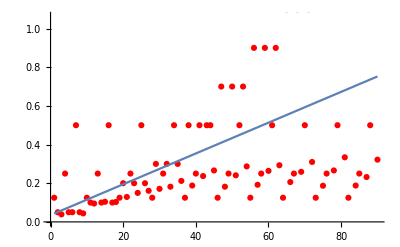

```mathematica
Show[ListPlot[%282,PlotStyle->Red],Plot[%285[x],{x,1,90}]]
```

```mathematica
%285["BasisFunctions"]
```

{1,x}

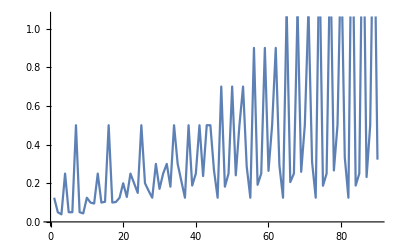

```mathematica
ListLinePlot[%282]
```

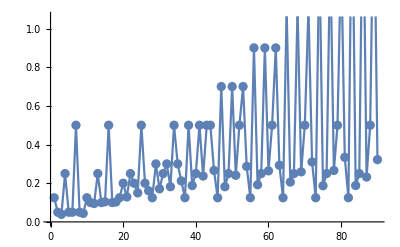

```mathematica
ListLinePlot[%282,Mesh->All]
```

```mathematica
TableForm[%265]
```

0.125 | 0.05 | 0.039
0.25 | 0.05 | 0.05
0.5 | 0.05 | 0.044
0.125 | 0.1 | 0.095
0.25 | 0.1 | 0.104
0.5 | 0.1 | 0.103
0.125 | 0.2 | 0.129
0.25 | 0.2 | 0.15
0.5 | 0.2 | 0.161
0.125 | 0.3 | 0.171
0.25 | 0.3 | 0.182
0.5 | 0.3 | 0.212
0.125 | 0.5 | 0.188
0.25 | 0.5 | 0.237
0.5 | 0.5 | 0.266
0.125 | 0.7 | 0.182
0.25 | 0.7 | 0.241
0.5 | 0.7 | 0.287
0.125 | 0.9 | 0.192
0.25 | 0.9 | 0.264
0.5 | 0.9 | 0.293
0.125 | 1.1 | 0.206
0.25 | 1.1 | 0.259
0.5 | 1.1 | 0.31
0.125 | 1.4 | 0.187
0.25 | 1.4 | 0.266
0.5 | 1.4 | 0.334
0.125 | 1.8 | 0.188
0.25 | 1.8 | 0.232
0.5 | 1.8 | 0.322

```mathematica
LinearModelFit[%277,{x,y},{x,y}]
```

FittedModel[0.069407+0.1924 x+0.100628 y]

```mathematica
%278["BestFitParameters"]
```

{0.069407,0.1924,0.100628}

```mathematica
%278["BestFit"]
```

0.069407+0.1924 x+0.100628 y

```mathematica
%278["BasisFunctions"]
```

{1,x,y}

```mathematica
ListPointPlot3D[%265]
```

-Graphics3D-

```mathematica
Transpose[%265]
```

{{0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5},{0.05,0.05,0.05,0.1,0.1,0.1,0.2,0.2,0.2,0.3,0.3,0.3,0.5,0.5,0.5,0.7,0.7,0.7,0.9,0.9,0.9,1.1,1.1,1.1,1.4,1.4,1.4,1.8,1.8,1.8},{0.039,0.05,0.044,0.095,0.104,0.103,0.129,0.15,0.161,0.171,0.182,0.212,0.188,0.237,0.266,0.182,0.241,0.287,0.192,0.264,0.293,0.206,0.259,0.31,0.187,0.266,0.334,0.188,0.232,0.322}}

```mathematica
LinearModelFit[%269,{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29},{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29}]
```

LinearModelFit::rank: The rank of the design matrix 3 is less than the number of terms 30 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[-0.0688663+«34»+0.0408011 x9]

```mathematica
%272["BestFitParameters"]
```

{-0.0688663,0.200062,0.164218,0.162128,-0.437267,-0.082389,0.0756454,-0.126467,-0.0611879,0.0408011,-0.0567823,-0.0027137,0.0240918,0.110477,0.0512193,0.0512076,0.161827,0.109983,0.0825295,0.153111,0.111085,0.100369,0.137741,0.117971,0.100196,0.129926,0.109815,0.0939574,0.109917,0.10434}

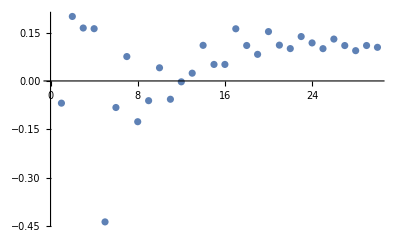

```mathematica
ListPlot[%274]
```

```mathematica
%272["BasisFunctions"]
```

{1,x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29}

```mathematica
LinearModelFit[%269,{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29},{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29}]
```

LinearModelFit::rank: The rank of the design matrix 3 is less than the number of terms 30 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[-0.0688663+«34»+0.0408011 x9]

```mathematica
%270["BestFit"]
```

-0.0688663+0.200062 x1-0.0567823 x10-0.0027137 x11+0.0240918 x12+0.110477 x13+0.0512193 x14+0.0512076 x15+0.161827 x16+0.109983 x17+0.0825295 x18+0.153111 x19+0.164218 x2+0.111085 x20+0.100369 x21+0.137741 x22+0.117971 x23+0.100196 x24+0.129926 x25+0.109815 x26+0.0939574 x27+0.109917 x28+0.10434 x29+0.162128 x3-0.437267 x4-0.082389 x5+0.0756454 x6-0.126467 x7-0.0611879 x8+0.0408011 x9

```mathematica
Flatten[%265]
```

{0.125,0.05,0.039,0.25,0.05,0.05,0.5,0.05,0.044,0.125,0.1,0.095,0.25,0.1,0.104,0.5,0.1,0.103,0.125,0.2,0.129,0.25,0.2,0.15,0.5,0.2,0.161,0.125,0.3,0.171,0.25,0.3,0.182,0.5,0.3,0.212,0.125,0.5,0.188,0.25,0.5,0.237,0.5,0.5,0.266,0.125,0.7,0.182,0.25,0.7,0.241,0.5,0.7,0.287,0.125,0.9,0.192,0.25,0.9,0.264,0.5,0.9,0.293,0.125,1.1,0.206,0.25,1.1,0.259,0.5,1.1,0.31,0.125,1.4,0.187,0.25,1.4,0.266,0.5,1.4,0.334,0.125,1.8,0.188,0.25,1.8,0.232,0.5,1.8,0.322}

```mathematica
LinearModelFit[%266,{1,x},x]
```

FittedModel[0.0352145+0.00796696 x]

```mathematica
Show[ListPlot[%266,PlotStyle->Red],Plot[%267[x],{x,1,90}]]
```

-Graphics-

```mathematica
Transpose[{v
```

```mathematica
Flatten[vNADS]
```

{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}

```mathematica
Fit[{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322},{1,x,x^2,x^3},x]
```

0.0638563+0.0213986 x-0.00116623 x^2+0.0000230962 x^3

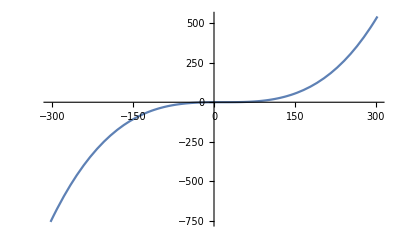

```mathematica
Plot[0.06385630498533723+0.021398623843476832 x-0.001166234895717822 x^2+0.000023096237517489963 x^3,{x,-302.96750148192064,302.96750148192064}]
```

```mathematica
DistributionFitTest[{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322},Automatic,"HypothesisTestData"]["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.273036 | 0.688558
Baringhaus-Henze | 0.137081 | 0.666977
Cramér-von Mises | 0.0296759 | 0.856004
Jarque-Bera ALM | 5.90428 | 0.0646594
Mardia Combined | 5.90428 | 0.0646594
Mardia Kurtosis | 1.35491 | 0.175446
Mardia Skewness | 1.75124 | 0.185721
Pearson χ^2 | 3.81818 | 0.701265
Shapiro-Wilk | 0.95872 | 0.237758

```mathematica
Fit[{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322},{1,x},x]
```

0.111013+0.00553576 x

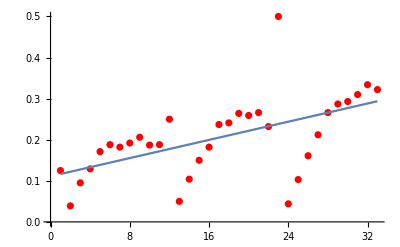

```mathematica
Show[ListPlot[{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322},PlotStyle->Red],Plot[0.11101325757575757+0.005535762032085561 x,{x,1,33}]]
```

```mathematica
LinearModelFit[{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322},{1,x},x]
```

FittedModel[0.111013+0.00553576 x]

```mathematica
Show[ListPlot[{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322},PlotStyle->Red],Plot[%252[x],{x,1,33}]]
```

-Graphics-

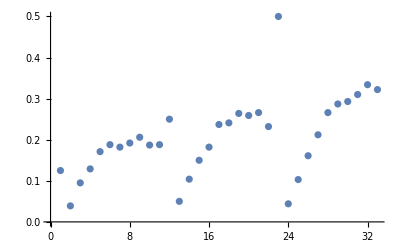

```mathematica
ListPlot[{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}]
```

```mathematica
SortBy[vNADS,Last]
```

{{0.125,{0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188}},{0.5,{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}},{0.25,{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}}}

```mathematica
Flatten[vNADS]
```

{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}

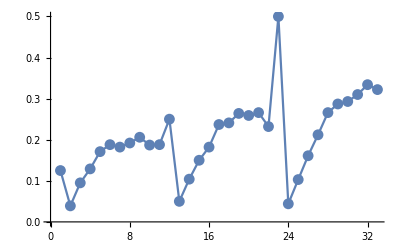

```mathematica
ListLinePlot[{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322},Mesh->All]
```

```mathematica
{{0.125,v125},{0.25,v250},{0.5,v500}}
```

{{0.125,{0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188}},{0.25,{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}},{0.5,{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}}}

```mathematica
Map[Length,%237,{2}]
```

{{0,10},{0,10},{0,10}}

```mathematica
Flatten[%237]
```

{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}

```mathematica
ListPlot[{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}]
```

-Graphics-

```mathematica
Flatten[vNADS]
```

{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}

```mathematica
{0.125,v125,0.25,v250,0.5,v500}
```

{0.125,{0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188},0.25,{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232},0.5,{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}}

```mathematica
Flatten[{0.125,{0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188},0.25,{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232},0.5,{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}}]
```

{0.125,0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188,0.25,0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232,0.5,0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}

```mathematica
Transpose[{cGAP,vNADS[[2]]}]
```

Transpose::nmtx: The first two levels of {{0.05,0.1,0.2,0.3,0.5,0.7,0.9,1.1,1.4,1.8},{0.25,{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}}} cannot be transposed.

Transpose[{{0.05,0.1,0.2,0.3,0.5,0.7,0.9,1.1,1.4,1.8},{0.25,{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}}}]

```mathematica
Data4=Flatten[{Transpose[{cNAD[[1]],cGAP,vNAD[[1]]}],Transpose[{cNAD[[2]],cGAP,vNAD[[2]]}],Transpose[{cNAD[[3]],cGAP,vNAD[[3]]}]},{2,1}]
```

{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}

```mathematica
ANOVA[{Data4},{x,y},{x,y}]
```

ANOVA[{{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}},{x,y},{x,y}]

```mathematica
ANOVA[{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322},{x,y},{x,y}]
```

ANOVA[{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322},{x,y},{x,y}]

```mathematica
Simplify[%181]
```

ANOVA[{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322},{x,y},{x,y}]

```mathematica
ANOVA[{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}]
```

ANOVA[{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}]

```mathematica
ANOVA[{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}]
```

ANOVA[{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}]

```mathematica
%181{x,y}
```

{ANOVA^({0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0},{1,0})[{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322},{x,y},{x,y}]+ANOVA^({0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{1,0},{0,0})[{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322},{x,y},{x,y}],ANOVA^({0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0},{0,1})[{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322},{x,y},{x,y}]+ANOVA^({0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,1},{0,0})[{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322},{x,y},{x,y}]}

```mathematica
Simplify[%176]
```

ANOVA[{{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}},{x,y},{x,y}]

```mathematica
Regress[{{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}},x,x]
```

```mathematica
Regress[{{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}}]
```

Regress[{{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}}]

```mathematica
Simplify[%411]
```

Regress[{{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}},x,x]

```mathematica
Simplify[%178]
```

Regress[{{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}}},x,x]

```mathematica
InverseFunction[Function[{x},%179]][x]
```

InverseFunction[Function[{x},%179]][x]

```mathematica
ClearAll
```

ClearAll

```mathematica
V0=(Subscript[V, max]×cGAP ×v125)/(Subscript[K, MGAP]×v125+Subscript[K, MNAD]×cGAP+v125 ×cGAP);
Rules = {Subscript[V, max]->k1 k2 k3 k4 k5 Etot, Subscript[K, MNAD]->cGAP2/cGAPNAD,Subscript[K, MGAP]->cNAD2/cGAPNAD};V0/.Rules
```

(Etot GAP k1 k2 k3 k4 k5 NAD)/((cGAP2 GAP)/cGAPNAD+(cNAD2 NAD)/cGAPNAD+GAP NAD)

```mathematica
nlmfit=NonlinearModelFit[test1,{V0,Subscript[V, max]≥0,Subscript[K, MGAP]≥0,Subscript[K, MNAD]≥0 }, {Subscript[V, max],Subscript[K, MGAP],Subscript[K, MNAD]},{cGAP,v125}];
```

General::ivar: {0.05,0.1,0.2,0.3,0.5,0.7,0.9,1.1,1.4,1.8} is not a valid variable.

```mathematica
vNAD={v125,v250,v500}
```

{{0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188},{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232},{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}}

```mathematica
ListPointPlot3D[Data4]
```

-Graphics3D-

```mathematica
nonLinearModelFit[Data4,{x,y},{x,y}]
```

nonLinearModelFit[{{0.125,0.05,0.039},{0.25,0.05,0.05},{0.5,0.05,0.044},{0.125,0.1,0.095},{0.25,0.1,0.104},{0.5,0.1,0.103},{0.125,0.2,0.129},{0.25,0.2,0.15},{0.5,0.2,0.161},{0.125,0.3,0.171},{0.25,0.3,0.182},{0.5,0.3,0.212},{0.125,0.5,0.188},{0.25,0.5,0.237},{0.5,0.5,0.266},{0.125,0.7,0.182},{0.25,0.7,0.241},{0.5,0.7,0.287},{0.125,0.9,0.192},{0.25,0.9,0.264},{0.5,0.9,0.293},{0.125,1.1,0.206},{0.25,1.1,0.259},{0.5,1.1,0.31},{0.125,1.4,0.187},{0.25,1.4,0.266},{0.5,1.4,0.334},{0.125,1.8,0.188},{0.25,1.8,0.232},{0.5,1.8,0.322}},{x,y},{x,y}]

```mathematica
%110["DesignMatrix"]
```

{{1.,0.125,0.05},{1.,0.25,0.05},{1.,0.5,0.05},{1.,0.125,0.1},{1.,0.25,0.1},{1.,0.5,0.1},{1.,0.125,0.2},{1.,0.25,0.2},{1.,0.5,0.2},{1.,0.125,0.3},{1.,0.25,0.3},{1.,0.5,0.3},{1.,0.125,0.5},{1.,0.25,0.5},{1.,0.5,0.5},{1.,0.125,0.7},{1.,0.25,0.7},{1.,0.5,0.7},{1.,0.125,0.9},{1.,0.25,0.9},{1.,0.5,0.9},{1.,0.125,1.1},{1.,0.25,1.1},{1.,0.5,1.1},{1.,0.125,1.4},{1.,0.25,1.4},{1.,0.5,1.4},{1.,0.125,1.8},{1.,0.25,1.8},{1.,0.5,1.8}}

```mathematica
ListPointPlot3D[%174]
```

-Graphics3D-

```mathematica
Show[Plot3D[%110[x,y],{x,0.125,0.5},{y,0.05,1.8}],Graphics3D[{Red,Point/@Data4}]]
```

-Graphics3D-

```mathematica
%110["AdjustedRSquared"]
```

0.599378

```mathematica
%110["CovarianceMatrix"]
```

{{0.000546017,-0.00107646,-0.000201906},{-0.00107646,0.00369072,-8.2164×10^-19},{-0.000201906,-8.2164×10^-19,0.000286392}}

```mathematica
%110["ANOVATableMeaANOVAnSquares"]
```

FittedModel::notprop: ANOVATableMeaANOVAnSquares is not a known property for FittedModel[0.069407+0.1924 x+0.100628 y]. Use FittedModel[0.069407+0.1924 x+0.100628 y]["Properties"] for a list of properties.

FittedModel[0.069407+0.1924 x+0.100628 y][ANOVATableMeaANOVAnSquares]

```mathematica
%5469["BestFit"]
```

%5469[BestFit]

```mathematica
ANOVA
```

ANOVA

```mathematica
Manipulate[Plot[0.06940697182536493+0.10062840875834737 (b+mx)+0.19240000000000052 x,{x,-6.,6.}],{b,-6.,6.},{mx,-2,2}]
```

```mathematica
%5469["ANOVATable"]
```

%5469[ANOVATable]

```mathematica
%5469["ANOVATableMeanSquares"]
```

%5469[ANOVATableMeanSquares]

```mathematica
Show[Plot3D[%5469[x,y],{x,0.125,0.5},{y,0.05,1.8}],Graphics3D[{Red,Point/@Data4}]]
```

-Graphics3D-

```mathematica
Show[%5470,Boxed->False]
```

Show::gtype: Out is not a type of graphics.

Show[%5470,Boxed→False]

```mathematica
Show[%5470,Boxed->False]
```

Show::gtype: Out is not a type of graphics.

Show[%5470,Boxed→False]

```mathematica
Show[%5471,ViewPoint->{-∞,0,0}]
```

Show::gtype: Out is not a type of graphics.

Show[%5471,ViewPoint→{-∞,0,0}]

```mathematica
ListPointPlot3D[Data4]
```

-Graphics3D-

```mathematica
Show[%5465,ViewPoint->Front]
```

Show::gtype: Out is not a type of graphics.

Show[%5465,ViewPoint→Front]

```mathematica
Show[%5466,ViewPoint->Right]
```

Show::gtype: Out is not a type of graphics.

Show[%5466,ViewPoint→Right]

```mathematica
Transpose[Data4]
```

{{0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5,0.125,0.25,0.5},{0.05,0.05,0.05,0.1,0.1,0.1,0.2,0.2,0.2,0.3,0.3,0.3,0.5,0.5,0.5,0.7,0.7,0.7,0.9,0.9,0.9,1.1,1.1,1.1,1.4,1.4,1.4,1.8,1.8,1.8},{0.039,0.05,0.044,0.095,0.104,0.103,0.129,0.15,0.161,0.171,0.182,0.212,0.188,0.237,0.266,0.182,0.241,0.287,0.192,0.264,0.293,0.206,0.259,0.31,0.187,0.266,0.334,0.188,0.232,0.322}}

```mathematica
cGAP={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800};
v125={0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188};
```

```mathematica
{0.05,0.1,0.2,0.3,0.5,0.7,0.9,1.1,1.4,1.8}
```

{0.05,0.1,0.2,0.3,0.5,0.7,0.9,1.1,1.4,1.8}

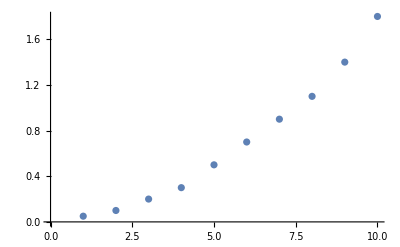

```mathematica
PlotA=ListPlot[{0.05,0.1,0.2,0.3,0.5,0.7,0.9,1.1,1.4,1.8}]
```

```mathematica
cGAP={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800};
```

```mathematica
v250={0.050,0.104,0.150,0.182,0.237,0.241,0.264,0.259,0.266,0.232};
```

```mathematica
{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}
```

{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}

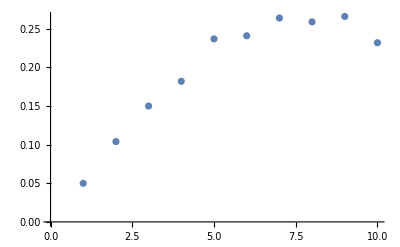

```mathematica
PlotB=ListPlot[{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}]
```

```mathematica
cGAP={0.050,0.100,0.200,0.300,0.500,0.700,0.900,1.100,1.400,1.800};
```

```mathematica
v500={0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.310,0.334,0.322};
```

```mathematica
{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}
```

{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}

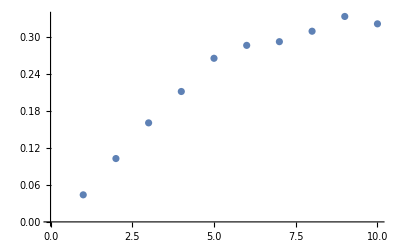

```mathematica
PlotC= ListPlot[{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}]
```

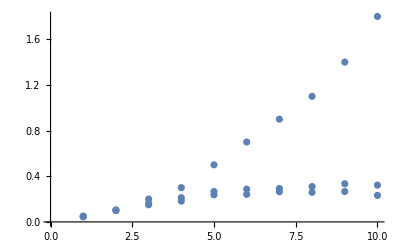

```mathematica
Show[PlotA, PlotB, PlotC]
```

```mathematica
icGAP=1/cGAP
```

{20.,10.,5.,3.33333,2.,1.42857,1.11111,0.909091,0.714286,0.555556}

```mathematica
iv125= 1/v125
```

{25.641,10.5263,7.75194,5.84795,5.31915,5.49451,5.20833,4.85437,5.34759,5.31915}

```mathematica
{25.641025641025642,10.526315789473685,7.751937984496124,5.847953216374268,5.319148936170213,5.4945054945054945,5.208333333333333,4.8543689320388355,5.347593582887701,5.319148936170213}
iv250 = 1/v250
```

{25.641,10.5263,7.75194,5.84795,5.31915,5.49451,5.20833,4.85437,5.34759,5.31915}

{20.,9.61538,6.66667,5.49451,4.21941,4.14938,3.78788,3.861,3.7594,4.31034}

```mathematica
iv500=1/v500
```

{22.7273,9.70874,6.21118,4.71698,3.7594,3.48432,3.41297,3.22581,2.99401,3.10559}

```mathematica
DataA=Transpose[{icGAP,iv125,v125}]
```

{{20.,25.641,0.039},{10.,10.5263,0.095},{5.,7.75194,0.129},{3.33333,5.84795,0.171},{2.,5.31915,0.188},{1.42857,5.49451,0.182},{1.11111,5.20833,0.192},{0.909091,4.85437,0.206},{0.714286,5.34759,0.187},{0.555556,5.31915,0.188}}

```mathematica
F4 =NonlinearModelFit[vNADS,{Subscript[κ, M]/Subscript[V, MAX]×S+1/Subscript[V, MAX],Subscript[V, MAX]>0,Subscript[κ, M]>0},{Subscript[V, MAX],Subscript[κ, M]},S]
```

NonlinearModelFit::fitd: First argument {{0.125,{0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188}},{0.25,{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}},{0.5,{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}}} in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[{{0.125,{0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188}},{0.25,{0.05,0.104,0.15,0.182,0.237,0.241,0.264,0.259,0.266,0.232}},{0.5,{0.044,0.103,0.161,0.212,0.266,0.287,0.293,0.31,0.334,0.322}}},{1/V_MAX+(S κ_M)/V_MAX,V_MAX>0,κ_M>0},{V_MAX,κ_M},S]

```mathematica
Subscript[κ, M]/Subscript[V, MAX]×S+1/Subscript[V, MAX] Subscript[κ, M]/Subscript[V, MAX]×S+  Subscript[V, O]=(Subscript[V, MAX]×S)/(Subscript[κ, M]+S)
```

Set::write: Tag Plus in V_O+(S κ_M)/V_MAX^2+(S κ_M)/V_MAX is Protected.

(S V_MAX)/(S+κ_M)

```mathematica
ListPointPlot3D[DataA]
```

-Graphics3D-

```mathematica
Transpose[DataA]
```

{{20.,10.,5.,3.33333,2.,1.42857,1.11111,0.909091,0.714286,0.555556},{25.641,10.5263,7.75194,5.84795,5.31915,5.49451,5.20833,4.85437,5.34759,5.31915},{0.039,0.095,0.129,0.171,0.188,0.182,0.192,0.206,0.187,0.188}}

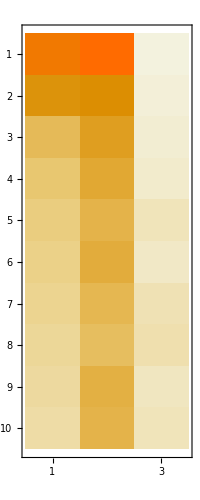

```mathematica
MatrixPlot[DataA]
```

```mathematica
Data= Transpose [{icGAP,iv125}]
```

{{20.,25.641},{10.,10.5263},{5.,7.75194},{3.33333,5.84795},{2.,5.31915},{1.42857,5.49451},{1.11111,5.20833},{0.909091,4.85437},{0.714286,5.34759},{0.555556,5.31915}}

```mathematica
F =NonlinearModelFit[DataA,{Subscript[κ, M]/Subscript[V, MAX]×S+1/Subscript[V, MAX],Subscript[V, MAX]>0,Subscript[κ, M]>0},{Subscript[V, MAX],Subscript[κ, M]},S]
```

NonlinearModelFit::fitc: Number of coordinates (2) is not equal to the number of variables (1).

NonlinearModelFit[{{20.,25.641,0.039},{10.,10.5263,0.095},{5.,7.75194,0.129},{3.33333,5.84795,0.171},{2.,5.31915,0.188},{1.42857,5.49451,0.182},{1.11111,5.20833,0.192},{0.909091,4.85437,0.206},{0.714286,5.34759,0.187},{0.555556,5.31915,0.188}},{1/V_MAX+(S κ_M)/V_MAX,V_MAX>0,κ_M>0},{V_MAX,κ_M},S]

```mathematica
F["ParameterTable"]
```

NonlinearModelFit::fitc: Number of coordinates (2) is not equal to the number of variables (1).

NonlinearModelFit[{{20.,25.641,0.039},{10.,10.5263,0.095},{5.,7.75194,0.129},{3.33333,5.84795,0.171},{2.,5.31915,0.188},{1.42857,5.49451,0.182},{1.11111,5.20833,0.192},{0.909091,4.85437,0.206},{0.714286,5.34759,0.187},{0.555556,5.31915,0.188}},{1/V_MAX+(S κ_M)/V_MAX,V_MAX>0,κ_M>0},{V_MAX,κ_M},S][ParameterTable]

```mathematica
%4464["BestFit"]
```

%4464[BestFit]

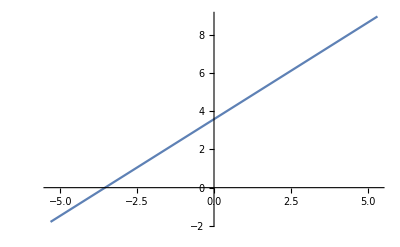

```mathematica
Plot[3.580844617012584+1.0099869721152794 S,{S,-5.318154663192826,5.318154663192826}]
```

General::ivar: -1.99955 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

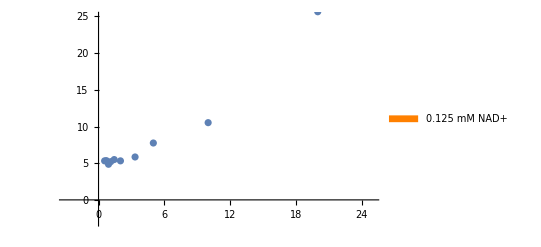

```mathematica
pp1=Show[ListPlot[Data,PlotRange->{{-3,25},{-3,25}}],Plot[F[S],{S,-2,Max[icGAP]},PlotStyle->{{Orange,PointSize[Medium]}},Frame->True,PlotLegends->SwatchLegend[{Orange}, {"0.125 mM NAD+"}],PlotLabel->Style["    Ping-Pong Mechanism"], AxesLabel->{ "[1/GAP],(1/mM","1/Vo,(min/AU)"},LabelStyle->Directive[14,Black]]]
```

Plot::nonopt: Options expected (instead of ListPlot[Data]) beyond position 2 in Plot[F[S],{S,-2,Max[icGAP]},ListPlot[Data]]. An option must be a rule or a list of rules.

Show::gcomb: Could not combine the graphics objects in ….

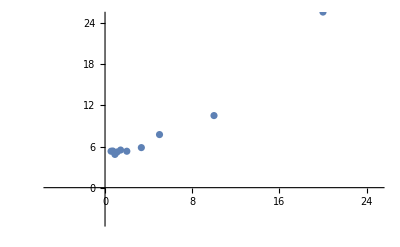
Show[-Graphics-,Plot[F[S],{S,-2,Max[icGAP]},ListPlot[Data]],PlotStyle→{{RGBColor[1, 0.5, 0],PointSize[Medium]}},Frame→True,PlotLegends→,PlotLabel→    Ping-Pong Mechanism,AxesLabel→{[1/GAP],(1/mM,1/Vo,(min/AU)},LabelStyle→Directive[14,GrayLevel[0]]]

```mathematica
Show[ListPlot[Data,PlotRange->{{-5,25},{-5,25}}],Plot[F[S],{S,-2,Max[icGAP]},ListPlot[Data]],PlotStyle->{{RGBColor[1, 0.5, 0],PointSize[Medium]}},Frame->True,PlotLegends->,PlotLabel->"    Ping-Pong Mechanism",AxesLabel->{"[1/GAP],(1/mM","1/Vo,(min/AU)"},LabelStyle->Directive[14,GrayLevel[0]]]
```

```mathematica
ListPlot[%4458]
```

ListPlot::lpn: %4458 is not a list of numbers or pairs of numbers.

ListPlot[%4458]

```mathematica
Data2=Transpose[{icGAP,iv250}]
```

{{20.,20.},{10.,9.61538},{5.,6.66667},{3.33333,5.49451},{2.,4.21941},{1.42857,4.14938},{1.11111,3.78788},{0.909091,3.861},{0.714286,3.7594},{0.555556,4.31034}}

```mathematica
F1 =NonlinearModelFit[Data2,{Subscript[κ, M]/Subscript[V, MAX]×S+1/Subscript[V, MAX],Subscript[V, MAX]>0,Subscript[κ, M]>0},{Subscript[V, MAX],Subscript[κ, M]},S]
```

FittedModel[2.92184+0.813407 S]

```mathematica
F1["AdjustedRSquared"]
```

0.992562

```mathematica
F1["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
V_MAX | 0.34225 | 0.0328604 | 10.4153 | 6.2595×10^-6
κ_M | 0.278389 | 0.036164 | 7.69796 | 0.0000575456

```mathematica
F1["BestFit"]
```

2.92184+0.813407 S

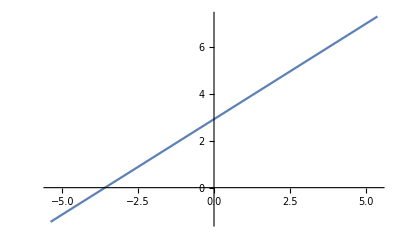

```mathematica
Plot[2.9218383391764697+0.813407360966559 S,{S,-5.38814586526085,5.38814586526085}]
```

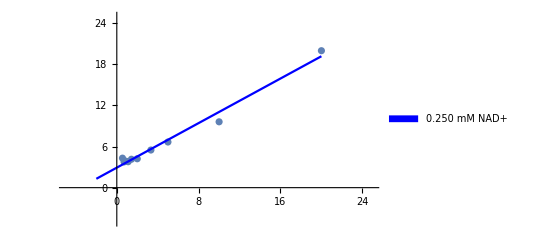

```mathematica
pp2=Show[ListPlot[Data2,PlotRange->{{-5,25},{-5,25}}],Plot[F1[S],{S,-2,Max[icGAP]},PlotStyle->{{Blue,PointSize[Medium]}},Frame->True,PlotLegends->SwatchLegend[{Blue}, {"0.250 mM NAD+"}],PlotLabel->Style["    Ping-Pong Mechanism"], AxesLabel->{ "[1/GAP],(1/mM","1/Vo,(min/AU)"},LabelStyle->Directive[14,Black]]]
```

```mathematica
Data3=Transpose[{icGAP,iv500}]
```

{{20.,22.7273},{10.,9.70874},{5.,6.21118},{3.33333,4.71698},{2.,3.7594},{1.42857,3.48432},{1.11111,3.41297},{0.909091,3.22581},{0.714286,2.99401},{0.555556,3.10559}}

```mathematica
V0=(Subscript[V, max] test1)/(Subscript[K, MGAP] vNAD+Subscript[K, MNAD] cGAP+test1);
Rules = {Subscript[V, max]->k1 k2 k3 k4 k5 Etot, Subscript[K, MNAD]->cGAP/cGAPNAD,Subscript[K, MGAP]->cNAD/cGAPNAD};V0/.Rules
```

Thread::tdlen: Objects of unequal length in «1» cannot be combined.

Thread::tdlen: Objects of unequal length in «1»+{«1»}+{{0.0025/cGAPNAD,0.005/cGAPNAD,0.01/cGAPNAD,0.015/cGAPNAD,0.025/cGAPNAD,(«21»)/cGAPNAD,0.045/cGAPNAD,0.055/cGAPNAD,0.07/cGAPNAD,0.09/cGAPNAD},{«1»},«7»,{«1»}} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{{(0.125 Etot k1 k2 k3 k4 k5)/1,(0.05 Etot k1 k2 k3 k4 k5)/({1}+{1}+{1}),(0.039 Etot k1 k2 k3 k4 k5)/({1}+{1}+{{0.0025/cGAPNAD,9},8,{1}})},8,{1}}
 |  |  |  |

```mathematica
F3 =NonlinearModelFit[test1,{(Subscript[V, max] GAP NAD)/(Subscript[K, MGAP] NAD+Subscript[K, MNAD] GAP+NAD GAP),Subscript[V, MAX]>0,Subscript[K, MGAP]>0,Subscript[K, MNAD]>0},{Subscript[V, MAX],Subscript[K, MNAD],Subscript[K, MGAP]},GAP, NAD]
```

NonlinearModelFit::nonopt: Options expected (instead of NAD) beyond position 4 in NonlinearModelFit[{{0.125,0.05,0.039},{0.125,0.1,0.095},{0.125,0.2,0.129},{0.125,0.3,0.171},{0.125,0.5,0.188},{0.125,0.7,0.182},{0.125,0.9,0.192},{0.125,1.1,0.206},{0.125,1.4,0.187},{0.125,1.8,0.188}},«3»,NAD]. An option must be a rule or a list of rules.

NonlinearModelFit[{{0.125,0.05,0.039},{0.125,0.1,0.095},{0.125,0.2,0.129},{0.125,0.3,0.171},{0.125,0.5,0.188},{0.125,0.7,0.182},{0.125,0.9,0.192},{0.125,1.1,0.206},{0.125,1.4,0.187},{0.125,1.8,0.188}},{(GAP NAD V_max)/(GAP NAD+NAD K_MGAP+GAP K_MNAD),V_MAX>0,K_MGAP>0,K_MNAD>0},{V_MAX,K_MNAD,K_MGAP},GAP,NAD]

```mathematica
F3["ParameterTable"]
```

NonlinearModelFit[{{0.125,0.05,0.039},{0.125,0.1,0.095},{0.125,0.2,0.129},{0.125,0.3,0.171},{0.125,0.5,0.188},{0.125,0.7,0.182},{0.125,0.9,0.192},{0.125,1.1,0.206},{0.125,1.4,0.187},{0.125,1.8,0.188}},{(GAP NAD V_max)/(GAP NAD+NAD K_MGAP+GAP K_MNAD),V_MAX>0,K_MGAP>0,K_MNAD>0},{V_MAX,K_MNAD,K_MGAP},GAP,NAD][ParameterTable]

```mathematica
F3["BestFit"]
```

NonlinearModelFit[{{0.125,0.05,0.039},{0.125,0.1,0.095},{0.125,0.2,0.129},{0.125,0.3,0.171},{0.125,0.5,0.188},{0.125,0.7,0.182},{0.125,0.9,0.192},{0.125,1.1,0.206},{0.125,1.4,0.187},{0.125,1.8,0.188}},{(GAP NAD V_max)/(GAP NAD+NAD K_MGAP+GAP K_MNAD),V_MAX>0,K_MGAP>0,K_MNAD>0},{V_MAX,K_MNAD,K_MGAP},GAP,NAD][BestFit]

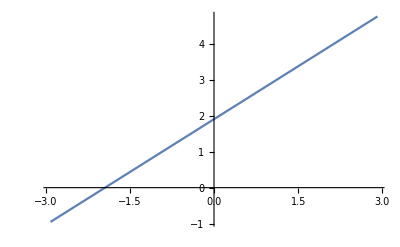

```mathematica
Plot[1.9078516277351896+0.9825933928185534 S,{S,-2.912473727707268,2.912473727707268}]
```

NonlinearModelFit::nonopt: Options expected (instead of NAD) beyond position 4 in NonlinearModelFit[{{0.125,0.05,0.039},{0.125,0.1,0.095},{0.125,0.2,0.129},{0.125,0.3,0.171},{0.125,0.5,0.188},{0.125,0.7,0.182},{0.125,0.9,0.192},{0.125,1.1,0.206},{0.125,1.4,0.187},{0.125,1.8,0.188}},«3»,NAD]. An option must be a rule or a list of rules.

General::stop: Further output of NonlinearModelFit::nonopt will be suppressed during this calculation.

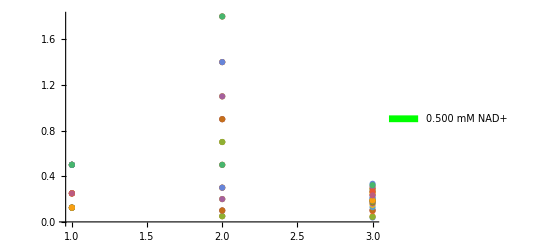

```mathematica
pp3=Show[ListPlot[Data4,PlotRange->Full],Plot[F3[S],{S,-10,Max[icGAP]},PlotStyle->{{Green,PointSize[Medium]}},Frame->True,PlotLegends->SwatchLegend[{Green}, {"0.500 mM NAD+"}],PlotLabel->Style["    Ping-Pong Mechanism"], AxesLabel->{ "[1/GAP],(1/mM","1/Vo,(min/AU)"},LabelStyle->Directive[14,Black]]]
```

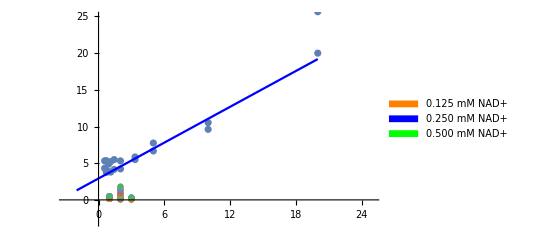

```mathematica
Show[pp1,pp2,pp3]
```

```mathematica
Plot[3.580844617012584+1.0099869721152794 S,S]
```

Plot::pllim: Range specification S is not of the form {x, xmin, xmax}.

Plot[3.58084+1.00999 S,S]